```mathematica
dir=NotebookDirectory[]
SetDirectory[dir];
```

/Users/hallermann/Desktop/twopool EGTA/out/

## import

File number: 1        ----------------------------------------------------------------------------------------------

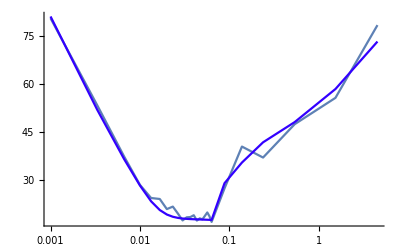

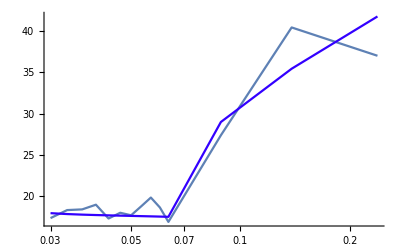

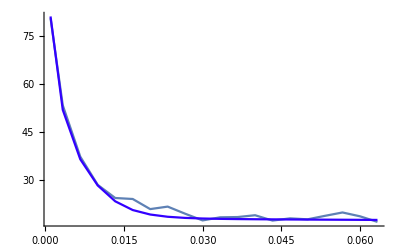

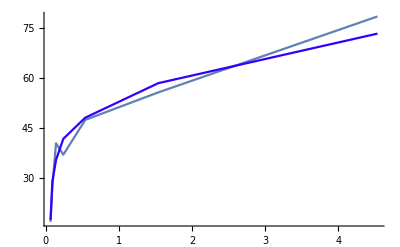

```mathematica
time300=Flatten[Import["time300.txt","Table"]];
time300[[1]]+=0.001;
tmp300=Import["apAmp300.txt","Table"];
tmpSim300=Import["apAmp300Sim.txt","Table"];
tmpexpo0300=Import["nR_300.txt","Table"];
tmpexpo1300=Import["n1_300.txt","Table"];
tmpexpo2300=Import["n2_300.txt","Table"];
tmpexpo4300=Import["p1_300.txt","Table"];
tmpexpo5300=Import["p2_300.txt","Table"];


numFiles=Length[tmp300[[1,All]]];

t300t1=10;
t300t2=23;
plR={All,All};
train=20;

For[i=1,i≤numFiles,i+=1,
(*For[i=numFiles-3,i≤numFiles,i+=1,*)
(*For[i=1,i≤numFiles,i+=1,*)
amp300=tmp300[[All,i]];
ampSim300=tmpSim300[[All,i]];


Print["File number: ",i,"        ----------------------------------------------------------------------------------------------"];

(*log*)
tmp1=ListLogLinearPlot[Transpose[{time300,amp300}],PlotRange->All,Joined->True,DisplayFunction -> Identity];
tmp2=ListLogLinearPlot[Transpose[{time300,ampSim300}],PlotRange->All,Joined->True,PlotStyle->Hue[0.7],DisplayFunction -> Identity];
gr300=Show[{tmp1,tmp2},PlotRange->plR,DisplayFunction -> Identity];
(*log part*)
tmp1=ListLogLinearPlot[Take[Transpose[{time300,amp300}],{t300t1,t300t2}],PlotRange->All,Joined->True,DisplayFunction -> Identity];
tmp2=ListLogLinearPlot[Take[Transpose[{time300,ampSim300}],{t300t1,t300t2}],PlotRange->All,Joined->True,PlotStyle->Hue[0.7],DisplayFunction -> Identity];
gr300part=Show[{tmp1,tmp2},PlotRange->plR,DisplayFunction -> Identity];
(*train*)
tmp1=ListPlot[Take[Transpose[{time300,amp300}],train],PlotRange->All,Joined->True,DisplayFunction -> Identity];
tmp2=ListPlot[Take[Transpose[{time300,ampSim300}],train],PlotRange->All,Joined->True,PlotStyle->Hue[0.7],DisplayFunction -> Identity];
gr300tr=Show[{tmp1,tmp2},PlotRange->plR,DisplayFunction -> Identity];
(*after train*)
tmp1=ListPlot[Take[Transpose[{time300,amp300}],{train,Length[time300]}],PlotRange->All,Joined->True,DisplayFunction -> Identity];
tmp2=ListPlot[Take[Transpose[{time300,ampSim300}],{train,Length[time300]}],PlotRange->All,Joined->True,PlotStyle->Hue[0.7],DisplayFunction -> Identity];
gr300rec=Show[{tmp1,tmp2},PlotRange->plR,DisplayFunction -> Identity];


Print[Show[{gr300}]];
Print[Show[{gr300part}]];
Print[Show[{gr300tr}]];
Print[Show[{gr300rec}]]
];
```

## show rates and chi2

```mathematica
tmp=Import["rates.txt","Table"];
Print[{{"U2","U1","chi2"},Flatten[tmp,1]}//MatrixForm];
```

(U2 | U1 | chi2
0.778462 | 0.216327 | 0.287064)